## 1. Calcul du tenseur de Riemann

### 1.1 Définitions en géométrie de Kerr

```mathematica
coord={t,r,x,ϕ};
gdd={{-(-2 M r+r^2+a^2 x^2)/(r^2+a^2 x^2),0,0,(2 a M r (-1+x^2))/(r^2+a^2 x^2)},{0,(r^2+a^2 x^2)/(a^2-2 M r+r^2),0,0},{0,0,(r^2+a^2 x^2)/(1-x^2),0},{(2 a M r (-1+x^2))/(r^2+a^2 x^2),0,0,-((-1+x^2) (r^4+a^4 x^2+a^2 r (2 M+r-2 M x^2+r x^2)))/(r^2+a^2 x^2)}};
```

```mathematica
Ydd={{0,-a x,-a r,0},{a x,0,0,a^2 x (-1+x^2)},{a r,0,0,-r (a^2+r^2)},{0,-a^2 x (-1+x^2),r (a^2+r^2),0}};
```

```mathematica
sqrtdetg=r^2+a^2 x^2;
```

```mathematica
RGtensors[gdd,coord,{0,0}]
```

gdd = (-(-2 M r+r^2+a^2 x^2)/(r^2+a^2 x^2) | 0 | 0 | (2 a M r (-1+x^2))/(r^2+a^2 x^2)
0 | (r^2+a^2 x^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | (r^2+a^2 x^2)/(1-x^2) | 0
(2 a M r (-1+x^2))/(r^2+a^2 x^2) | 0 | 0 | -((-1+x^2) (r^4+a^4 x^2+a^2 r (2 M+r-2 M x^2+r x^2)))/(r^2+a^2 x^2))

LineElement = ((r^2+a^2 x^2) d[r]^2)/(a^2-2 M r+r^2)-((-2 M r+r^2+a^2 x^2) d[t]^2)/(r^2+a^2 x^2)-((r^2+a^2 x^2) d[x]^2)/(-1+x^2)+(4 a M r (-1+x^2) d[t] d[ϕ])/(r^2+a^2 x^2)-((-1+x^2) (2 a^2 M r+a^2 r^2+r^4+a^4 x^2-2 a^2 M r x^2+a^2 r^2 x^2) d[ϕ]^2)/(r^2+a^2 x^2)

gUU = (-(2 a^2 M r+a^2 r^2+r^4+a^4 x^2-2 a^2 M r x^2+a^2 r^2 x^2)/((a^2-2 M r+r^2) (r^2+a^2 x^2)) | 0 | 0 | -(2 a M r)/((a^2-2 M r+r^2) (r^2+a^2 x^2))
0 | (a^2-2 M r+r^2)/(r^2+a^2 x^2) | 0 | 0
0 | 0 | -(-1+x^2)/(r^2+a^2 x^2) | 0
-(2 a M r)/((a^2-2 M r+r^2) (r^2+a^2 x^2)) | 0 | 0 | -(-2 M r+r^2+a^2 x^2)/((a^2-2 M r+r^2) (-1+x^2) (r^2+a^2 x^2)))

gUU computed in 0. sec

Gamma computed in 0.032 sec

Riemann(dddd) computed in 0.031 sec

RUddd not computed

Ricci computed in 0. sec

Weyl tensor not computed

Ricci Flat

All tasks completed in 0.0625

```mathematica
Rdd//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
GUdd=Simplify[GUdd];
```

```mathematica
Rdddd=Simplify[Rdddd];
```

```mathematica
epsdddd=Table[Signature[{a,b,c,d}],{a,1,4},{b,1,4},{c,1,4},{d,1,4}]sqrtdetg;
epsUUUU=-Table[Signature[{a,b,c,d}],{a,1,4},{b,1,4},{c,1,4},{d,1,4}]/sqrtdetg;
epsddUU=Raise[epsdddd,{3,4}];
```

```mathematica
sYdd=-1/2 gdd. Contract[epsUUUU . Ydd,{3,4}] . gdd//Simplify;
sYUU=gUU . sYdd . gUU//Simplify;
```

```mathematica
Z=-1/4 Tr[Ydd . sYUU]//Simplify
```

-a r x

```mathematica
Zjd=covD[Z]
```

{0,-a x,-a r,0}

```mathematica
Zjdd=covD[Zjd];
Zjddd=covD[Zjdd];
```

```mathematica
Yddjd=covD[Ydd,{}];
Yddjd+Transpose[Yddjd,{1,3,2}]//Simplify
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
YUd=gUU . Ydd//Simplify;
YUU=YUd.gUU//Simplify;
KUd=YUd . YUd//Simplify;
Kdd=Ydd . YUd//Simplify;
KUU=KUd . gUU//Simplify;
```

```mathematica
xiU={1,0,0,0};
xid=gdd.xiU;
```

```mathematica
xiSquared:=xid.xiU//Simplify;
```

```mathematica
Kddjd=covD[Kdd,{}];
```

```mathematica
RUddd=gUU.Rdddd;
RUUdd=Transpose[multiDot[RUddd,gUU,{2,1}],{1,3,4,2}];
RUUdU=multiDot[RUUdd,gUU,{4,1}];
RUUUU=multiDot[RUUdU,gUU,{3,1}];
RUdUd = multiDot[RUddd,gUU, {3,1}];
sRUUdd=1/2 multiDot[epsUUUU,Rdddd,{1,1},{2,2}]//Simplify;
RsddUU=1/2 Transpose[ multiDot[epsUUUU,Rdddd,{1,3},{2,4}],{3,4,1,2}]//Simplify;
```

```mathematica
sRUddd=Lower[sRUUdd,{2}]//Simplify;
```

```mathematica
sRdddd=gdd.sRUddd//Simplify;
Rsdddd=Lower[RsddUU,{3,4}]//Simplify;
sRsUUdd=1/2 multiDot[epsUUUU,Rsdddd,{1,1},{2,2}]//Simplify;
sRsdddd=Lower[sRsUUdd,{1,2}]//Simplify;
```

```mathematica
pU={pt,pr,pθ,pϕ};
SU={St,Sr,Sθ,Sϕ};
```

```mathematica
pd = gdd . pU;
```

```mathematica
K=Contract[gUU.Kdd,{1,2}]//FullSimplify;
```

```mathematica
RUdddjd=covD[RUddd,{1}];
Rddddjd=covD[Rdddd];
sRUdddjd=covD[sRUddd,{1}];
```

```mathematica
Yddjd=covD[Ydd];
Yddjdd=covD[Yddjd];
```

## 2. Hamiltonien quadrupolaire

### 2.1 Métrique de Scwharzschild et variables dynamiques

```mathematica
(*On prépare tout pour métrique de SCHW et theta = pi/2, la présence du "S" dénote ce cadre*)
gddS = gdd /.{a->0,x->0} //FullSimplify;
gUUS = gUU/.{a->0,x->0} //FullSimplify;
RUUUUS = RUUUU/.{a->0,x->0} //FullSimplify;
RUdUdS = RUdUd/.{a->0,x->0} //FullSimplify;
RUUddS = RUUdd/.{a->0,x->0} //FullSimplify;
RddddS = Rdddd/.{a->0,x->0} //FullSimplify;
sRddddS = sRdddd/.{a->0,x->0} //FullSimplify;
(*On défnit les variables dynamique dans SCHW*)
pdS={pt,pr,0,pϕ};
pUS = gUUS. pdS ;

dotxSU = {dott,dotr,0,dotϕ};
dotxSd = gddS.dotxSU //FullSimplify;

μ = Sqrt[-pUS.pdS]
```

√(-pr^2 (1-(2 M)/r)-pϕ^2/r^2-(pt^2 r)/(2 M-r))

### 2.2 Hamiltonien

```mathematica
(*Partie quadrupolaire électrique*)
ESdd=-pUS.RddddS.pUS/μ^2 //FullSimplify;
ESUU=gUUS.ESdd.gUUS//FullSimplify;
ESUd = gUUS.ESdd//FullSimplify;
ESquaredS=Contract[ESdd.ESUU,{1,2}]//FullSimplify;
(*Partie quadrupolaire magnétique*)
BSdd = -pUS.sRddddS.pUS/μ^2 //FullSimplify;
BSUU = gUUS.BSdd.gUUS //FullSimplify;
BSquaredS = Contract[BSdd.BSUU,{1,2}] //FullSimplify;
```

```mathematica
HgS = (1/2)pdS.gUUS.pdS;
HquadS = -(μ/12)*(cE*ESquaredS + 4*cB*BSquaredS)//FullSimplify;
HS =  HgS + HquadS
```

1/2 (pr^2 (1-(2 M)/r)+pϕ^2/r^2+(pt^2 r)/(2 M-r))-(M^2 √(pr^2 (-1+(2 M)/r)-pϕ^2/r^2-(pt^2 r)/(2 M-r)) (4 cE M^2 pϕ^4+8 (12 cB+cE) M^3 pr^2 pϕ^2 r-4 cE M pϕ^4 r+(16 cE M^4 pr^4-12 (12 cB+cE) M^2 pr^2 pϕ^2+cE pϕ^4) r^2-2 M (16 cE M^2 pr^4-(12 cB+cE) (3 pr^2-pt^2) pϕ^2) r^3+(8 cE M^2 pr^2 (3 pr^2-pt^2)-(12 cB+cE) (pr-pt) (pr+pt) pϕ^2) r^4+8 cE M pr^2 (-pr^2+pt^2) r^5+cE (pr^2-pt^2)^2 r^6))/(2 r^6 (4 M^2 pr^2 r+pϕ^2 r+(pr-pt) (pr+pt) r^3-2 M (pϕ^2+2 pr^2 r^2))^2)

#### Comparaison des Hamiltoniens

```mathematica
f:=1-2M/r;
AA:=pϕ^2/r^2;
RR:=-pt^2/f+f pr^2;
Hdraftg = (AA+RR)/2;
Hdraftquad = M^2/(2r^6)(3(4 cB+cE)AA RR-cE(AA+RR)^2)/(-(AA+RR))^(3/2)//Simplify;
Hdraft=Hdraftg + Hdraftquad//Simplify
```

1/2 (pr^2 (1-(2 M)/r)+pϕ^2/r^2+(pt^2 r)/(2 M-r)+(M^2 ((3 (4 cB+cE) pϕ^2 (pr^2 (1-(2 M)/r)+(pt^2 r)/(2 M-r)))/r^2-cE (pr^2 (1-(2 M)/r)+pϕ^2/r^2+(pt^2 r)/(2 M-r))^2))/((pt^2/(1-(2 M)/r)+pr^2 (-1+(2 M)/r)-pϕ^2/r^2)^(3/2) r^6))

```mathematica
Hdraft-HS//FullSimplify
```

0

### 2.3 Changement de variables

```mathematica
$Assumptions:={pt≏̸ 0,μT>0, M>0, ρ>3,e>0,l>0,eSquared>0,lSquared>0};
```

```mathematica
(*Hamiltonien adimensionnalisé*)
HadimS = HS/.{r->M*ρ,pt->-μT*e,pϕ->μT*M*l,pr->μT*pR,cE->cμ*M^4*μT,cB->cσ*M^4*μT}//FullSimplify
```

(μT^2 ((ρ^5 (l^2 (-2+ρ)+ρ (pR^2 (-2+ρ)^2-e^2 ρ^2))^3)/(-2+ρ)+√(-l^2+(ρ (-pR^2 (-2+ρ)^2+e^2 ρ^2))/(-2+ρ)) (12 cσ l^2 (-2+ρ) ρ (pR^2 (-2+ρ)^2-e^2 ρ^2)+cμ (-l^4 (-2+ρ)^2+l^2 (-2+ρ) ρ (pR (-2+ρ)-e ρ) (pR (-2+ρ)+e ρ)-(pR^2 (-2+ρ)^2 ρ-e^2 ρ^3)^2))))/(2 ρ^7 (l^2 (-2+ρ)+ρ (pR^2 (-2+ρ)^2-e^2 ρ^2))^2)

### 2.4 Équation de Hamilton-Jacobi (w’[r])

```mathematica
EqHamJacSCWH = HadimS + (μT^2)/2/.pR->Sqrt[W];
```

#### Solution géodésique

```mathematica
SolgeoW = Solve[EqHamJacSCWH==0/.{cμ->0,cσ->0,W->W0},W0]//FullSimplify//Flatten
```

{W0→(-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ))/((-2+ρ)^2 ρ)}

```mathematica
Wgeo = W0/.SolgeoW;
```

#### Solution électrique

```mathematica
EqHamJacSCWHδWelec = EqHamJacSCWH/.cσ->0/.W->W0 + cμ δWelec/.SolgeoW[[1]]//Simplify;
EqHamJacSCWHδWelecLin = Series[EqHamJacSCWHδWelec ,{cμ,0,1}];
SolδWelec = Solve[EqHamJacSCWHδWelecLin==0,δWelec][[1]]//FullSimplify
```

{δWelec→(3 l^4+3 l^2 ρ^2+ρ^4)/((-2+ρ) ρ^9)}

#### Solution magnétique

```mathematica
EqHamJacSCWHδWmag = EqHamJacSCWH/.cμ->0/.W->W0 + cσ δWmag/.SolgeoW[[1]]//Simplify;
EqHamJacSCWHδWmagLin = Series[EqHamJacSCWHδWmag ,{cσ,0,1}];
SolδWmag = Solve[EqHamJacSCWHδWmagLin==0,δWmag][[1]]//FullSimplify
```

{δWmag→(12 l^2 (l^2+ρ^2))/((-2+ρ) ρ^9)}

#### Solution générale quadrupolaire

```mathematica
SolquadW = W0 + cμ δWelec+ cσ δWmag /.SolgeoW/.SolδWelec/.SolδWmag;
Solquadwr = Normal[Series[Series[SolquadW^2,{cμ,0,1}],{cσ,0,1}]]
```

(24 cσ l^2 (l^2+ρ^2) (-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ)))/((-2+ρ)^3 ρ^10)+((-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ))^2)/((-2+ρ)^4 ρ^2)+cμ ((24 cσ l^2 (l^2+ρ^2) (3 l^4+3 l^2 ρ^2+ρ^4))/((-2+ρ)^2 ρ^18)+(2 (3 l^4+3 l^2 ρ^2+ρ^4) (-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ)))/((-2+ρ)^3 ρ^10))

#### Solution quadrupolaire

```mathematica
Solquadδwr= Solve[FullSimplify[Normal[Series[EqHamJacSCWH/.{cμ->χ*cμ,cσ->χ*cσ}/.{W->(Sqrt[Wgeo]+χ*δw)^2},{χ,0,1}]]==0]/.χ->1, δw]//FullSimplify
```

{{δw→(3 (cμ+4 cσ) l^4+3 (cμ+4 cσ) l^2 ρ^2+cμ ρ^4)/(2 ρ^(17/2) √(-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ)))}}

```mathematica
Solquadwr2 = Sqrt[Wgeo] + δw/.Solquadδwr
```

{(3 (cμ+4 cσ) l^4+3 (cμ+4 cσ) l^2 ρ^2+cμ ρ^4)/(2 ρ^(17/2) √(-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ)))+√((-l^2 (-2+ρ)+ρ^2 (2+(-1+e^2) ρ))/((-2+ρ)^2 ρ))}

### 2.5 Équations de mouvement circulaire

```mathematica
(*Remarquons que pour le cas circulaire dotr=0 est équivalent à pr = 0*)
eqdotr= dotxSU[[2]]==D[HS,pdS[[2]]]//Simplify
```

dotr+(pr (2 M-r) (-12 cB M^2 pϕ^2 (2 M-r) (4 M^2 pr^2 r-2 pϕ^2 r+(pr^2-pt^2) r^3+4 M (pϕ^2-pr^2 r^2))+2 r^6 √(pr^2 (-1+(2 M)/r)-pϕ^2/r^2-(pt^2 r)/(2 M-r)) (4 M^2 pr^2 r+pϕ^2 r+(pr^2-pt^2) r^3-2 M (pϕ^2+2 pr^2 r^2))^2+cE M^2 (16 M^4 pr^4 r^2-5 pϕ^4 r^2+5 (pr^2-pt^2) pϕ^2 r^4+(pr^2-pt^2)^2 r^6-8 M^3 (5 pr^2 pϕ^2 r+4 pr^4 r^3)-4 M^2 (5 pϕ^4-15 pr^2 pϕ^2 r^2+2 pr^2 (-3 pr^2+pt^2) r^4)+2 M (10 pϕ^4 r+5 (-3 pr^2+pt^2) pϕ^2 r^3+4 pr^2 (-pr^2+pt^2) r^5))))/(2 r^7 √(pr^2 (-1+(2 M)/r)-pϕ^2/r^2-(pt^2 r)/(2 M-r)) (4 M^2 pr^2 r+pϕ^2 r+(pr^2-pt^2) r^3-2 M (pϕ^2+2 pr^2 r^2))^2)==0

#### Solution géodésique

```mathematica
HgeoCirc = HadimS/.{cμ->0,cσ->0,pR->0,e->Sqrt[eSquared],l->Sqrt[lSquared]}//FullSimplify;
```

```mathematica
solGeoCirc = Solve[HgeoCirc==-μT^2/2 && D[HgeoCirc,ρ]==0,{eSquared,lSquared}]//FullSimplify
```

{{eSquared→(-2+ρ)^2/((-3+ρ) ρ),lSquared→ρ^2/(-3+ρ)}}

```mathematica
eGeo = Sqrt[eSquared]/.solGeoCirc[[1]][[1]];
lGeo = Sqrt[lSquared]/.solGeoCirc[[1]][[2]];
```

#### Solution quadrupolaire

```mathematica
HadimS
```

(μT^2 ((ρ^5 (l^2 (-2+ρ)+ρ (pR^2 (-2+ρ)^2-e^2 ρ^2))^3)/(-2+ρ)+√(-l^2+(ρ (-pR^2 (-2+ρ)^2+e^2 ρ^2))/(-2+ρ)) (12 cσ l^2 (-2+ρ) ρ (pR^2 (-2+ρ)^2-e^2 ρ^2)+cμ (-l^4 (-2+ρ)^2+l^2 (-2+ρ) ρ (pR (-2+ρ)-e ρ) (pR (-2+ρ)+e ρ)-(pR^2 (-2+ρ)^2 ρ-e^2 ρ^3)^2))))/(2 ρ^7 (l^2 (-2+ρ)+ρ (pR^2 (-2+ρ)^2-e^2 ρ^2))^2)

```mathematica
solCOM=Solve[FullSimplify[Normal[Series[{HadimS+μT^2/2,D[HadimS, ρ]}/.{cμ->χ*cμ,cσ->χ cσ,pR->0}/.{e->eGeo+χ δϵ,l->lGeo+χ δℓ},{χ,0,1}]]=={0,0}]/.{χ->1},{δϵ,δℓ}]//FullSimplify//Flatten
```

{δϵ→((-2+ρ) (12 cσ (-5+3 ρ)+cμ (3+ρ (-3+2 ρ))))/(2 (-3+ρ)^(5/2) ρ^(13/2)),δℓ→(48 cσ (-2+ρ)^2+cμ (-15+ρ (21+ρ (-13+3 ρ))))/(2 (-3+ρ)^(5/2) ρ^5)}

```mathematica
δϵquad = δϵ/.solCOM
δℓquad = δℓ/.solCOM
```

((-2+ρ) (12 cσ (-5+3 ρ)+cμ (3+ρ (-3+2 ρ))))/(2 (-3+ρ)^(5/2) ρ^(13/2))

(48 cσ (-2+ρ)^2+cμ (-15+ρ (21+ρ (-13+3 ρ))))/(2 (-3+ρ)^(5/2) ρ^5)

### 2.6 Potentiel effectif et ISCO

#### Géodésique

```mathematica
dotρgeo = D[HadimS,pR]/.pR->Solquadwr2/.{cμ->0,cσ->0,μT->1}//FullSimplify;
Veffgeo = (1/2)e^2-(1/2)dotρgeo^2 //FullSimplify
```

{((-2+ρ) (l^2+ρ^2))/(2 ρ^3)}

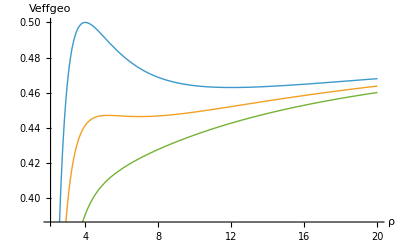

```mathematica
FVeffgeo[l_,ρ_]:=((-2+ρ) (l^2+ρ^2))/(2 ρ^3);
Plot[{FVeffgeo[4,ρ],FVeffgeo[3.5,ρ],FVeffgeo[3,ρ]},{ρ,2.1,20},AxesLabel->{"ρ","Veffgeo"},PlotStyle->Thick]
```

```mathematica
Solve[D[Veffgeo,ρ]==0,ρ]//FullSimplify
```

{{ρ→ConditionalExpression[1/2 l (l-√(-12+l^2)), l>2 √3]},{ρ→ConditionalExpression[1/2 l (l+√(-12+l^2)), l>2 √3]}}

```mathematica
ρmin[l_]:=1/2 l (l-√(-12+l^2));
```

```mathematica
lISCOgeo = 2 √3
ρISCOgeo = ρmin[lISCOgeo]
eISCOgeo = Sqrt[2*FVeffgeo[lISCOgeo,ρISCOgeo]]
```

2 √3

6

(2 √2)/3

#### Quadrupôle

```mathematica
dotρquad=D[HadimS,pR]/.pR->Solquadwr2/.{μT->1};
dotρquadLin = Normal[Series[Series[dotρquad,{cμ,0,1}],{cσ,0,1}]]//FullSimplify;
Veffquad = -(1/2)dotρquadLin^2 + e^2/2 //FullSimplify;
VeffquadLin = Normal[Series[Veffquad/.{cμ->χ*cμ,cσ->χ*cσ},{χ,0,1}]]/.χ->1//FullSimplify
```

{1/(2 ρ^13)((-2+ρ) ρ^10 (l^2+ρ^2)+cμ (-9 l^6 (-2+ρ)-e^2 ρ^7+3 l^4 ρ^2 (10-5 ρ+3 e^2 ρ)+l^2 ρ^4 (10-5 ρ+3 e^2 ρ))+12 cσ l^2 (-3 l^4 (-2+ρ)+l^2 ρ^2 (10-5 ρ+3 e^2 ρ)+ρ^4 (4+(-2+e^2) ρ)))}

```mathematica
FVeffquad[e_,l_,ρ_,cμ_,cσ_]:=1/(2 ρ^13)((-2+ρ) ρ^10 (l^2+ρ^2)+cμ (-9 l^6 (-2+ρ)-e^2 ρ^7+3 l^4 ρ^2 (10-5 ρ+3 e^2 ρ)+l^2 ρ^4 (10-5 ρ+3 e^2 ρ))+12 cσ l^2 (-3 l^4 (-2+ρ)+l^2 ρ^2 (10-5 ρ+3 e^2 ρ)+ρ^4 (4+(-2+e^2) ρ)));
```

```mathematica
(*Thèse Paul Ramond (6.8)*)
Rneutron = 0.1;
k2 = 0.10;
j2 = 0.019;
μ2Neutron = (2/3)Rneutron^5*k2
σ2Neutron = (1/48)Rneutron^5*j2
cμNeutron = (3/2)μ2Neutron;
cσNeutron = -2σ2Neutron;
```

6.66667×10^-7

3.95833×10^-9

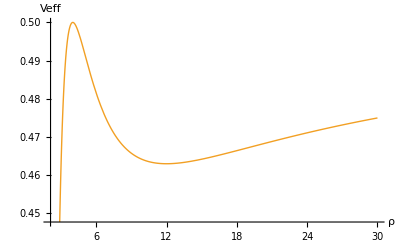

```mathematica
Plot[{FVeffgeo[1,4,ρ],FVeffquad[1,4,ρ,cμNeutron,cσNeutron]},{ρ,2.1,30},AxesLabel->{"ρ","Veff"},PlotStyle->Thick]
```

```mathematica
SolquadδISCO = Solve[Normal[Series[{D[VeffquadLin, ρ],D[D[VeffquadLin, ρ], ρ]}/.{cμ->χ*cμ,cσ->χ*cσ,ρ->ρISCOgeo + χ*δρ,l->lISCOgeo + χ*δl, e-> eISCOgeo + χ*δe},{χ,0,1}]]=={0,0}/.{χ->1},{δρ,δl}];
SolquadδeISCO = Solve[Normal[Series[e^2/2-FVeffquad[e,lISCOquad,ρISCOquad,cμ,cσ]/.{cμ->χ*cμ,cσ->χ*cσ,e-> eISCOgeo + χ*δe},{χ,0,1}]]==0/.{χ->1},{δe}];
```

```mathematica
ρISCOquad = ρISCOgeo + δρ/.SolquadδISCO
lISCOquad = lISCOgeo + δl/.SolquadδISCO
eISCOquad = eISCOgeo+δe/.SolquadδeISCO
```

{6+(37 cμ+112 cσ)/2916}

{2 √3+(97 √3 cμ+256 √3 cσ)/139968}

{(2 √2)/3+(19 cμ+52 cσ)/(209952 √2)}

### 2.7 Fréquence angulaire et redshift circulaire

```mathematica
$Assumptions:={cμ>0,cσ>0,ρ>2,M>0,r>2M};
```

#### Cas géodésique

```mathematica
Ωgeo = -(1/M)*(D[HadimS, l])*(D[HadimS, e])^(-1)/.pR->0/.{e->eGeo ,l->lGeo}/.{cμ->0,cσ->0,μT->1} //PowerExpand//FullSimplify
```

1/(M ρ^(3/2))

```mathematica
zgeo =  -(D[HadimS, e])^(-1)/.pR->0/.{e->eGeo ,l->lGeo}/.{cμ->0,cσ->0,μT->1} //PowerExpand//FullSimplify
```

√((-3+ρ)/ρ)

#### Cas quadrupolaire

```mathematica
deHinv = (D[HadimS, e])^(-1)/.pR->0/.{e->eGeo + δϵquad,l->lGeo +δℓquad}/.{cμ->χ*cμ,cσ->χ cσ};
deHinvlin = Normal[Series[ deHinv,{χ,0,1}]]/.χ->1//PowerExpand//FullSimplify
```

(3 cμ (-2+ρ)^2-2 (-3+ρ)^2 ρ^6+12 cσ (-5+2 ρ))/(2 μT^2 (-3+ρ)^(3/2) ρ^(13/2))

```mathematica
dlH = D[HadimS, l]/.pR->0/.{e->eGeo + δϵquad,l->lGeo +δℓquad}/.{cμ->χ*cμ,cσ->χ cσ};
dlHlin = Normal[Series[ dlH,{χ,0,1}]]/.χ->1//PowerExpand//FullSimplify
```

(μT^2 (3 cμ (-2+ρ)^3+2 (-3+ρ)^2 ρ^6+12 cσ (-2+ρ) (-5+2 ρ)))/(2 (-3+ρ)^(5/2) ρ^7)

```mathematica
Ω =  -(1/M)deHinvlin*dlHlin/.{cμ->χ*cμ,cσ->χ cσ};
ΩLin = Normal[Series[ Ω,{χ,0,1}]]/.χ->1//PowerExpand//FullSimplify;
δΩ = ΩLin-Ωgeo //FullSimplify;
Ωquad = Ωgeo +δΩ
```

1/(M ρ^(3/2))+(3 (cμ (-2+ρ)^2+4 cσ (-5+2 ρ)))/(2 M (-3+ρ) ρ^(15/2))

```mathematica
zshift = -(μT^2)* deHinvlin/.{cμ->χ*cμ,cσ->χ cσ};
zLin = Normal[Series[ zshift,{χ,0,1}]]/.χ->1//PowerExpand//FullSimplify;
δz = zLin-zgeo //FullSimplify;
zquad = zgeo +δz
```

√((-3+ρ)/ρ)-(3 (cμ (-2+ρ)^2+4 cσ (-5+2 ρ)))/(2 (-3+ρ)^(3/2) ρ^(13/2))

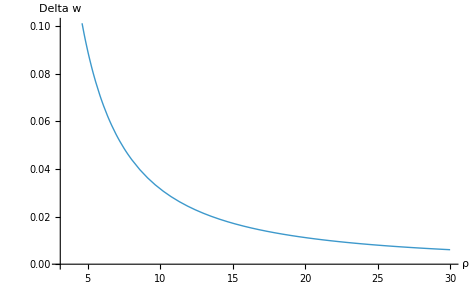

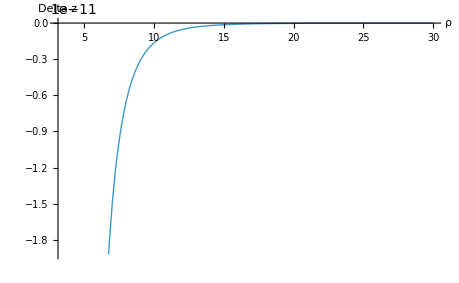

```mathematica
FδΩquad[ρ_,M_,cμ_,cσ_]:=1/(M ρ^(3/2))+(3 (cμ (-2+ρ)^2+4 cσ (-5+2 ρ)))/(2 M (-3+ρ) ρ^(15/2));
Fδzquad[ρ_,cμ_,cσ_]:= -(3 (cμ (-2+ρ)^2+4 cσ (-5+2 ρ)))/(2 (-3+ρ)^(3/2) ρ^(13/2));
Plot[{FδΩquad[ρ,1,cμNeutron,cσNeutron]},{ρ,3.1,30},AxesLabel->{"ρ","Delta w"},PlotStyle->Thick]
Plot[{Fδzquad[ρ,cμNeutron,cσNeutron]},{ρ,3.1,30},AxesLabel->{"ρ","Delta z"},PlotStyle->Thick]
```